```mathematica
path=NotebookDirectory[];
dataDirectories={"rabi_and_lmg_optimizations_20190228","rabi_and_lmg_optimizations_different_constraints_20190228"};
(*datafiles=FileNames[FileNameJoin@{path,"rabi*.csv"}]*)
```

```mathematica
SetOptions[EvaluationNotebook[],ShowGroupOpener->True];
SetOptions[$FrontEndSession,ShowGroupOpener->True];
SetOptions[$FrontEnd,ShowGroupOpener->True];
ClearAll@t;
bangRampParametersToProtocol[tf_,y0_,t1_,y1_,y2_]:=Piecewise[{{y0,0≤t≤t1},{(y2-y1)(t-t1)/(tf-t1)+y1,t1<t≤tf}}];
bangRampParametersToProtocol[dataset_Dataset]:=bangRampParametersToProtocol@@List@@Normal@dataset@{"tf","y0","t1","y1","y2"};
doubleBangParametersToProtocol[tf_,y0_,t1_,y1_]:=Piecewise[{{y0,0≤t≤t1},{y1,t1<t≤tf}}];
doubleBangParametersToProtocol[dataset_Dataset]:=doubleBangParametersToProtocol@@List@@Normal@dataset@{"tf","y0","t1","y1"};
tripleBangParametersToProtocol[tf_,y1_,y2_,y3_,t1_,t2_]:=Piecewise[{
{y1,0≤t≤t1},
{y2,t1<t≤t2},
{y3,t2<t}
}];
tripleBangParametersToProtocol[dataset_Dataset]:=tripleBangParametersToProtocol@@List@@Normal@dataset@{"tf","y1","y2","y3","t1","t2"};
CRABParametersToProtocol[tf_,frequencies_,Ak_,Bk_,y0_,y1_]:=Module[{baseline,normalisingPulse,pulseCorrection,finalProtocol},
normalisingPulse[t_]:=0.1 t (t-tf);
pulseCorrection[t_]:=1+normalisingPulse[t]*Total@Plus[
Ak*Sin[2Pi Range[Length@frequencies](1+frequencies)*t/tf],
Bk*Cos[2Pi Range[Length@frequencies](1+frequencies)*t/tf]
];
baseline[t_]:=Interpolation[{{0,y0},{tf,y1}},InterpolationOrder->1][t];
finalProtocol[t_]:=baseline[t]*pulseCorrection[t];
finalProtocol[t]
];
CRABParametersToProtocol[dataset_Dataset]:=With[{numFreqs=Length@dataset[Keys][Select[StringTake[#,UpTo@3]=="nuk"&]]},
With[{pars=List@@@Normal@dataset@{
"tf",
Table["nuk"<>ToString@k,{k,numFreqs}],
Table["A"<>ToString@k,{k,numFreqs}],
Table["B"<>ToString@k,{k,numFreqs}],
"y0","y1"
}},
CRABParametersToProtocol@@pars
(*CRABParametersToProtocol@@List@@Normal@dataset@{"tf","y1","y2","y3","t1","t2"}*)
]];
protocolFromDatafile[dataset_,filename_]:=Which[
StringCases[filename,"bangramp"]≠{},
bangRampParametersToProtocol@dataset,
StringCases[filename,"doublebang"]≠{},
doubleBangParametersToProtocol@dataset,
StringCases[filename,"crab"]≠{},
(* if initial and final pulse heights were not in the dataset, try to infer from the name *)
If[Not@KeyExistsQ[dataset,"y0"],
With[{criticalParValue=Which[
StringContainsQ[filename,"rabi"],5,
StringContainsQ[filename,"lmg"],1
]},
CRABParametersToProtocol@dataset@Append[<|"y0"->0,"y1"->criticalParValue|>]
],
(* otherwise, just use the dataset as is *)
CRABParametersToProtocol@dataset
],
StringCases[filename,"triplebang"]≠{},
tripleBangParametersToProtocol@dataset
];
```

```mathematica
csvTableToDataset[dataFromCSV_]:=Transpose@Dataset@Association@Thread[dataFromCSV⟦1⟧->Transpose@dataFromCSV⟦2;;⟧];
csvExplorer[filenames_]:=Manipulate[
With[{filename=FileBaseName@filenames⟦k⟧,dataset=csvTableToDataset@Import[filenames⟦k⟧]⟦All,2;;⟧},
Deploy@GraphicsRow[{
Deploy@Graphics[{
PointSize@0.014,RGBColor[0.368417, 0.506779, 0.709798],
MapIndexed[
EventHandler[Point@#1,
{"MouseClicked":>(solutionIndex=First@#2)}
]&,
List@@@Normal@dataset[All,{"tf","fid"}]
],
{Red,PointSize@0.02,Point@{List@@Normal@dataset[solutionIndex,{"tf","fid"}]}}
},
Frame->{{True,False},{True,False}},PlotRange->{All,Normal@dataset[All,"fid"][MinMax]},
AspectRatio->1/GoldenRatio
],
Plot[protocolFromDatafile[dataset@solutionIndex,filename],{t,0,dataset[solutionIndex,"tf"]},
PlotRange->{{0,All},{-10,10}},PlotLabel->"total time:"<>ToString@dataset[solutionIndex,"tf"]
]
},ImageSize->800,PlotLabel->filename]
],
{{k,1},Thread[Range[Length@filenames]->FileBaseName/@filenames]},
{{solutionIndex,1},1,Length@Import[filenames⟦k⟧]⟦2;;,2;;⟧,1,Appearance->"Labeled"},ControlPlacement->Right
];
ClearAll@csvExplorerLight;
csvExplorerLight[filenames_,yRange_:{-10,10}]:=Manipulate[
With[{filename=FileBaseName@filenames⟦k⟧,dataset=csvTableToDataset@Import[filenames⟦k⟧]⟦All,2;;⟧},
Deploy@GraphicsRow[{
Deploy@Graphics[{
PointSize@0.014,RGBColor[0.368417, 0.506779, 0.709798],
Point[List@@@Normal@dataset[All,{"tf","fid"}]],
{Red,PointSize@0.02,Point@{List@@Normal@dataset[solutionIndex,{"tf","fid"}]}}
},
Frame->{{True,False},{True,False}},PlotRange->{All,Normal@dataset[All,"fid"][MinMax]},
AspectRatio->1/GoldenRatio
],
With[{fun=protocolFromDatafile[dataset@solutionIndex,filename]},Plot[fun,{t,0,dataset[solutionIndex,"tf"]},
PlotRange->{{0,All},yRange},PlotLabel->"total time:"<>ToString@dataset[solutionIndex,"tf"]<>", fid: "<>ToString@dataset[solutionIndex,"fid"]
]]
},ImageSize->800,PlotLabel->filename]
],
{{k,1},Thread[Range[Length@filenames]->FileBaseName/@filenames]},
{{solutionIndex,1},1,Length@Import[filenames⟦k⟧]⟦2;;,2;;⟧,1,Appearance->"Labeled"},ControlPlacement->Right
];
```

## Visualize all results and corresponding protocols in rabi_and _lmg _optimizations _ 20190228

```mathematica
csvExplorer@FileNames[FileNameJoin@{path,dataDirectories⟦1⟧,"rabi*.csv"}]
```

```mathematica
csvExplorer@FileNames[FileNameJoin@{path,dataDirectories⟦1⟧,"lmg*.csv"}]
```

## Visualize all results and corresponding protocols in rabi_and _lmg _optimizations _different _constraints _ 20190228

```mathematica
csvExplorer@FileNames[FileNameJoin@{path,dataDirectories⟦2⟧,"rabi*.csv"}]
```

```mathematica
DynamicModule[{datafiles=FileNames[FileNameJoin@{path,dataDirectories⟦2⟧,"lmg*.csv"}]},
Manipulate[
With[{filename=FileBaseName@datafiles⟦k⟧,data=Import[datafiles⟦k⟧]⟦2;;,2;;⟧},
GraphicsRow[{
ListPlot[data⟦All,2⟧,PlotRange->{All,{0.7,1}},Joined->True,PlotMarkers->Automatic,
Epilog->{Red,PointSize@0.02,Point@{{solutionIndex,data⟦All,2⟧⟦solutionIndex⟧}}}
],
Plot[protocolFromDatafile[data⟦solutionIndex,All⟧,filename],{t,0,data⟦solutionIndex,1⟧},
PlotRange->{{0,4},{-7,7}},PlotLabel->"total time:"<>ToString@data⟦solutionIndex,1⟧
]
},ImageSize->800,PlotLabel->filename]
],
(*{{k,1},1,Length@datafiles,1,Appearance->"Labeled"},*)
{{k,1},Thread[Range[Length@datafiles]->FileBaseName/@datafiles]},
{{solutionIndex,1},1,Length@Import[datafiles⟦k⟧]⟦2;;,2;;⟧,1,Appearance->"Labeled"},ControlPlacement->Right
]]
```

## Visualize all results and corresponding protocols in lmg_different_spinnumbers_20190228

```mathematica
spinnumbersPath="lmg_different_spinnumbers_20190228";
DynamicModule[{datafiles=FileNames[FileNameJoin@{path,spinnumbersPath,"lmg*.csv"}]},
Manipulate[
With[{filename=FileBaseName@datafiles⟦k⟧,data=Import[datafiles⟦k⟧]⟦2;;,2;;⟧},
GraphicsRow[{
ListPlot[data⟦All,2⟧,PlotRange->{All,{0.7,1}},Joined->True,PlotMarkers->Automatic,
Epilog->{Red,PointSize@0.02,Point@{{solutionIndex,data⟦All,2⟧⟦solutionIndex⟧}}}
],
Plot[protocolFromDatafile[data⟦solutionIndex,All⟧,filename],{t,0,data⟦solutionIndex,1⟧},
PlotRange->{{0,4},All},PlotLabel->"total time:"<>ToString@data⟦solutionIndex,1⟧
]
},ImageSize->800,PlotLabel->filename]
],
(*{{k,1},1,Length@datafiles,1,Appearance->"Labeled"},*)
{{k,1},Thread[Range[Length@datafiles]->FileBaseName/@datafiles]},
{{solutionIndex,1},1,Length@Import[datafiles⟦k⟧]⟦2;;,2;;⟧,1,Appearance->"Labeled"},ControlPlacement->Right
]]
```

## Visualize all results and corresponding protocols in rabi_and _lmg _optimizations _crossingcriticalphase _ 20190305

```mathematica
data=Import[First@FileNames[FileNameJoin@{path,"rabi_and_lmg_optimizations_crossingcriticalphase_20190305","lmg*tf20.csv"}]]⟦;;3,2;;⟧
```

{{tf,fid,y0,t1,y1},{0.5,0.0000515264,2.,0.350474,-1.99998},{0.548872,0.0000723652,2.,0.388681,-1.99984}}

```mathematica
With[{data=Import[First@FileNames[FileNameJoin@{path,"rabi_and_lmg_optimizations_crossingcriticalphase_20190305","lmg*tf20.csv"}]]⟦2;;,2;;⟧},
data⟦165⟧
]
```

{8.51504,0.9802,1.10284,5.18851,1.47825}

```mathematica
csvExplorer@FileNames[FileNameJoin@{path,"rabi_and_lmg_optimizations_crossingcriticalphase_20190305","lmg*tf20.csv"}]
```

```mathematica
csvExplorer@FileNames[FileNameJoin@{path,"rabi_and_lmg_optimizations_crossingcriticalphase_20190305","lmg*tf10.csv"}]
```

## Triple bang results

```mathematica
csvExplorer@FileNames[FileNameJoin@{path,"rabi_and_lmg_optimizations_triplebamg_20190305","*.csv"}]
```

## Study saturated doublebang protocol for LMG

### Doesn’t change much changing the number of spins

{/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/rabi_and_lmg_optimizations_20190228/lmg_doublebang_powell.csv,/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/lmg_different_spinnumbers_20190228/lmg_doublebang_powell_100spins.csv,/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/lmg_different_spinnumbers_20190228/lmg_doublebang_powell_150spins.csv}

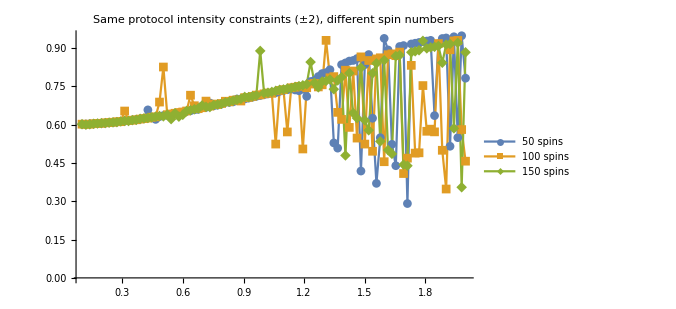

```mathematica
With[{data=Import[#]⟦2;;,2;;⟧&/@Echo@Prepend[
FileNames@FileNameJoin@{path,"lmg_different_spinnumbers_20190228","lmg_doublebang_powell*.csv"},
First@FileNames@FileNameJoin@{path,"rabi_and_lmg_optimizations_20190228","lmg_doublebang_powell*.csv"}
]},
With[{points=Map[{#⟦1⟧,#⟦4⟧/#⟦1⟧}&,data,{2}]},
ListPlot[points,
Joined->True,PlotRange->All,PlotMarkers->Automatic,PlotLegends->{"50 spins","100 spins","150 spins"},ImageSize->500,PlotLabel->"Same protocol intensity constraints (±2), different spin numbers"
]
]
]
```

```mathematica
Import[First@FileNames@FileNameJoin@{path,"rabi_and_lmg_optimizations_different_constraints_20190228","lmg_doublebang_powell*.csv"}]⟦;;5,2;;⟧//TableForm
```

tf | fid | y0 | t1 | y1
0.1 | 0.812697 | 2.99994 | 0.0573449 | -2.99995
0.119192 | 0.814446 | 3. | 0.0685015 | -2.99997
0.138384 | 0.816495 | 3. | 0.0795486 | -2.99986
0.157576 | 0.818819 | 2.99999 | 0.0922344 | -2.99992

```mathematica
Select[
Import[First@FileNames@FileNameJoin@{path,"rabi_and_lmg_optimizations_different_constraints_20190228","lmg_doublebang_powell*.csv"}]⟦2;;5,2;;⟧,
#⟦⟧
]
```

{}

```mathematica
DynamicModule[{datafiles=FileNames@FileNameJoin@{path,"rabi_and_lmg_optimizations_different_constraints_20190228","lmg_doublebang_powell*.csv"}},
Manipulate[
With[{filename=FileBaseName@datafiles⟦k⟧,
data=Select[#,#⟦4⟧/#⟦1⟧≥0.5&]&@Import[datafiles⟦k⟧]⟦2;;,2;;⟧
},
GraphicsRow[{
ListPlot[data⟦All,2⟧,PlotRange->{All,{0.7,1}},Joined->True,PlotMarkers->Automatic,
Epilog->{Red,PointSize@0.02,Point@{{solutionIndex,data⟦All,2⟧⟦solutionIndex⟧}}}
],
Plot[protocolFromDatafile[data⟦solutionIndex,All⟧,filename],{t,0,data⟦solutionIndex,1⟧},
PlotRange->{{0,4},{-10,10}},PlotLabel->"total time:"<>ToString@data⟦solutionIndex,1⟧
]
},ImageSize->800,PlotLabel->filename]
],
{{k,1},Thread[Range[Length@datafiles]->FileBaseName/@datafiles]},
{{solutionIndex,1},1,Length@Import[datafiles⟦k⟧]⟦2;;,2;;⟧,1,Appearance->"Labeled"},ControlPlacement->Top
]]
```

```mathematica
With[{data=Import[#]⟦2;;,2;;⟧&/@Echo@Prepend[
FileNames@FileNameJoin@{path,"rabi_and_lmg_optimizations_different_constraints_20190228","lmg_doublebang_powell*.csv"},
First@FileNames@FileNameJoin@{path,"rabi_and_lmg_optimizations_20190228","lmg_doublebang_powell*.csv"}
]},
With[{points=Map[{#⟦1⟧,#⟦4⟧/#⟦1⟧,#⟦3⟧/#⟦5⟧}&,data,{2}]},
Echo@Dimensions@points;
Graphics3D[{
Table[{Hue[k/3],Point@points⟦k⟧},{k,3}],
Opacity@0.4,InfinitePlane[{0,0,-1},{{1,0,0},{0,1,0}}]
},
Axes->True,AxesLabel->{"tf","t1/tf","y0/y1"},BoxRatios->1,
PlotRange->{All,All,{-40,40}},ImageSize->500,PlotLabel->"50 spins, different max protocol intensities"
]
]
]
```

{/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/rabi_and_lmg_optimizations_20190228/lmg_doublebang_powell.csv,/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/rabi_and_lmg_optimizations_different_constraints_20190228/lmg_doublebang_powell_bounds3.csv,/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/rabi_and_lmg_optimizations_different_constraints_20190228/lmg_doublebang_powell_bounds5.csv,/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/rabi_and_lmg_optimizations_different_constraints_20190228/lmg_doublebang_powell_bounds7.csv}

{4,100,3}

-Graphics3D-

```mathematica
Manipulate[
With[{data=Import[#]⟦2;;,2;;⟧&/@Prepend[
FileNames@FileNameJoin@{path,"rabi_and_lmg_optimizations_different_constraints_20190228","lmg_doublebang_powell*.csv"},
First@FileNames@FileNameJoin@{path,"rabi_and_lmg_optimizations_20190228","lmg_doublebang_powell*.csv"}
]},
With[{filteredData=Select[#,#⟦2⟧>1-10^-threshold&]&/@data},
With[{points=Map[{#⟦3⟧,#⟦4⟧,#⟦5⟧}&,filteredData,{2}]},
Echo@Dimensions@points;
Graphics3D[{
Table[{Hue[k/4],Point@points⟦k⟧},{k,{whichPlot}}],
Opacity@0.4,InfinitePlane[{0,0,-2},{{1,0,0},{0,1,0}}]
},
Axes->True,AxesLabel->{"y0","t1","y1"},BoxRatios->1,
PlotRange->{All,All,{-10,10}},ImageSize->500,PlotLabel->"50 spins, different max protocol intensities",RotationAction->"Clip"
]
]
]],
{{whichPlot,1},1,4,1,Appearance->"Labeled"},
{{threshold,1},0,8,1,Appearance->"Labeled"},ControlPlacement->Right
]
```

{/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/rabi_and_lmg_optimizations_20190228/lmg_doublebang_powell.csv,/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/rabi_and_lmg_optimizations_different_constraints_20190228/lmg_doublebang_powell_bounds3.csv,/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/rabi_and_lmg_optimizations_different_constraints_20190228/lmg_doublebang_powell_bounds5.csv,/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/rabi_and_lmg_optimizations_different_constraints_20190228/lmg_doublebang_powell_bounds7.csv}

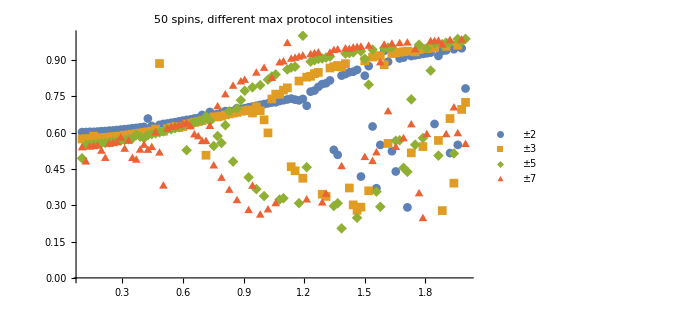

```mathematica
With[{data=Import[#]⟦2;;,2;;⟧&/@Echo@Prepend[
FileNames@FileNameJoin@{path,"rabi_and_lmg_optimizations_different_constraints_20190228","lmg_doublebang_powell*.csv"},
First@FileNames@FileNameJoin@{path,"rabi_and_lmg_optimizations_20190228","lmg_doublebang_powell*.csv"}
]},
With[{points=Map[{#⟦1⟧,#⟦4⟧/#⟦1⟧}&,data,{2}]},
ListPlot[points,
PlotRange->All,PlotMarkers->Automatic,PlotLegends->{"±2","±3","±5","±7"},ImageSize->500,PlotLabel->"50 spins, different max protocol intensities"
]
]
]
```

### Scans of all combinations of total time and t_1/t_f ratio for LMG

Use this to plot a ContourPlot for a single scan

```mathematica
With[{data=Import@First@FileNames@{FileNameJoin@{NotebookDirectory[],"lmg_doublebang_scans_20190301","*.csv"}}},
ListContourPlot[
data⟦2;;,2;;⟧,
ColorFunction->"TemperatureMap",PlotLegends->Automatic,Contours->Append[Range[0,1,0.05],0.99],
FrameLabel->{"tf","t1/tf"},PlotRangePadding->None,PerformanceGoal->"Quality"
]]
```

Plot a row of contour plots for several scans (same spin, different constraints)

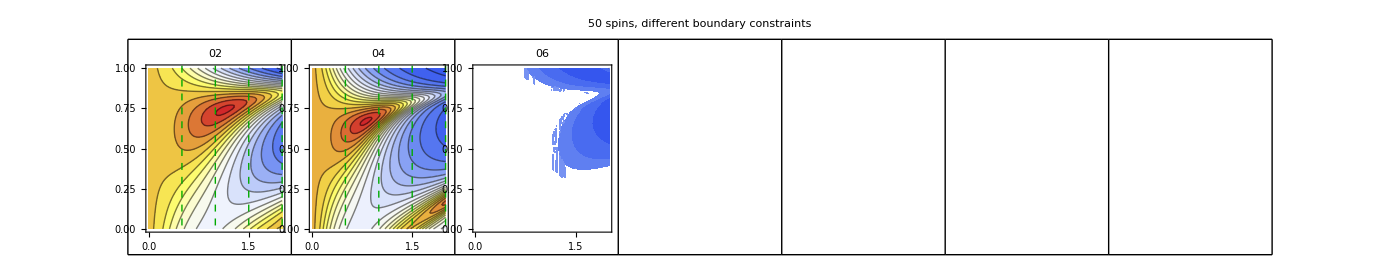

```mathematica
With[{datafiles=FileNames@{FileNameJoin@{NotebookDirectory[],"lmg_doublebang_scans_20190301","scan_50spins*.csv"}}},
With[{dataSets=Import/@datafiles},
GraphicsRow[Table[
ListContourPlot[
dataSets⟦idx⟧⟦2;;,2;;⟧,
ColorFunction->"TemperatureMap",Contours->Append[Range[0,1,0.05],0.99],
PlotRangePadding->None,PlotLabel->StringTake[FileBaseName@datafiles⟦idx⟧,-2],ImagePadding->None,ImageMargins->0,
Frame->True,Epilog->{Dashed,Thick,Darker@Green,Table[InfiniteLine@{{#,0},{#,1}}&@k,{k,{0.5,1,1.5,2}}]}
],
{idx,Length@dataSets}
],0,Frame->All,PlotLabel->"50 spins, different boundary constraints",ImageSize->1400]
]]
```

```mathematica
FileNames@{FileNameJoin@{NotebookDirectory[],"lmg_doublebang_scans_20190301","scan_50spins*.csv"}}
```

{/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/lmg_doublebang_scans_20190301/scan_50spins_bound002.csv,/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/lmg_doublebang_scans_20190301/scan_50spins_bound004.csv,/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/lmg_doublebang_scans_20190301/scan_50spins_bound006.csv,/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/lmg_doublebang_scans_20190301/scan_50spins_bound008.csv,/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/lmg_doublebang_scans_20190301/scan_50spins_bound010.csv,/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/lmg_doublebang_scans_20190301/scan_50spins_bound012.csv,/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/lmg_doublebang_scans_20190301/scan_50spins_bound014.csv,/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/lmg_doublebang_scans_20190301/scan_50spins_bound050.csv,/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/lmg_doublebang_scans_20190301/scan_50spins_bound100.csv}

0.259797-0.559064 x

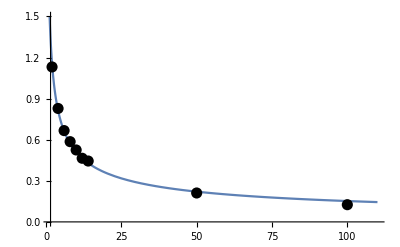
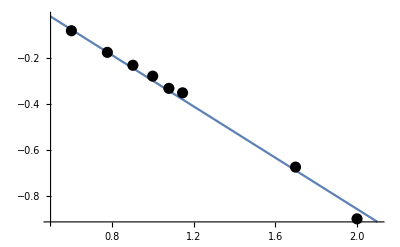

```mathematica
With[{datafiles=FileNames@{FileNameJoin@{NotebookDirectory[],"lmg_doublebang_scans_20190301","scan_50spins*.csv"}}},
With[{dataSets=Import[#]⟦2;;,2;;⟧&/@datafiles},
With[{maximalTimes=TakeLargestBy[#,#⟦3⟧&,1]⟦1,1⟧&/@dataSets},
With[{points=Table[{ToExpression@StringTake[#,{-7,-5}]&@datafiles⟦k⟧,maximalTimes⟦k⟧},{k,Length@maximalTimes}]},
Row@{
Plot[
Evaluate@Fit[points,{1,1/x^(1/2)},x],{x,.5,110},
PlotRange->{{1.5,110},{0,1.5}},ImageSize->400,
Epilog->{PointSize@0.02,Point@points}
],
Plot[
Evaluate@Echo@Fit[Log10@points,{1,x},x],{x,.5,2.1},
PlotRange->All,ImageSize->400,
Epilog->{PointSize@0.02,Point@Log10@points}
]
}
]]]]
```

```mathematica
Rationalize@0.15
```

3/20

```mathematica
1/6.
```

0.166667

```mathematica
vars={0.0,3.393351800554001,13.573407202216117,30.54016620498612,54.29362880886424,84.83379501385048,122.16066481994471,166.27423822714672,217.1745152354572,274.86149584487544,339.3351800554017,410.59556786703615,488.6426592797784,573.4764542936289,665.0969529085874,763.5041551246538,868.6980609418283,980.678670360111,1099.4459833795017,1225.0};
gs={0.,5.26315789,10.52631579,15.78947368,21.05263158,26.31578947,31.57894737,36.84210526,42.10526316,47.36842105,52.63157895,57.89473684,63.15789474,68.42105263,73.68421053,78.94736842,84.21052632,89.47368421,94.73684211,100.};
```

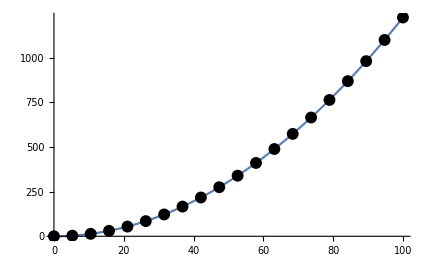

```mathematica
Plot[0.1225 x^2,{x,0,100},
Epilog->{PointSize@0.02,Point@Thread@{gs,vars}}
]
```

```mathematica
Fit[Log10@Rest@Thread@{gs,vars},{1,x},x]
```

-0.911864+2. x

```mathematica
Fit[Rest@Thread@{gs,vars},{1,x^2},x]
```

9.99283×10^-9+0.1225 x^2

```mathematica
With[{datafiles=FileNames@{FileNameJoin@{NotebookDirectory[],"lmg_doublebang_scans_20190301","scan_50spins*.csv"}}},
With[{dataSets=Import[#]⟦2;;,2;;⟧&/@datafiles},
With[{maximalPoints=TakeLargestBy[#,#⟦3⟧&,1]⟦1,;;2⟧&/@dataSets},
Table[
Join[maximalPoints⟦k⟧,{ToExpression@StringTake[#,{-7,-5}]&@datafiles⟦k⟧}],
{k,Length@maximalPoints}
]
]]]
```

{{1.13131,0.737374,2},{0.828283,0.676768,4},{0.666667,0.646465,6},{0.585859,0.636364,8},{0.525253,0.626263,10},{0.464646,0.616162,12},{0.444444,0.616162,14},{0.211055,0.571429,50},{0.125628,0.546366,100}}

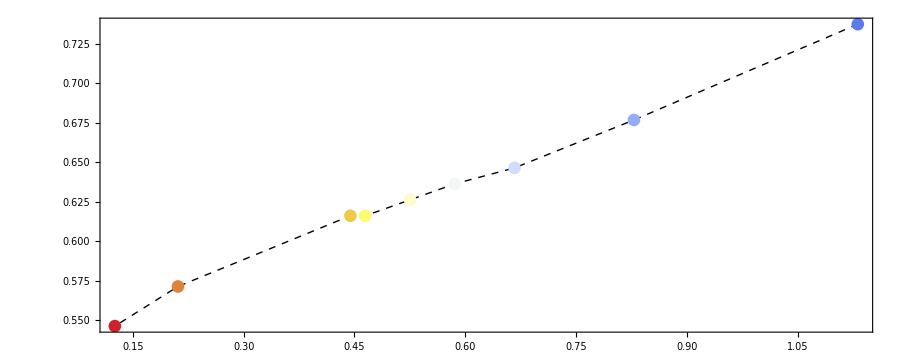

```mathematica
With[{datafiles=FileNames@{FileNameJoin@{NotebookDirectory[],"lmg_doublebang_scans_20190301","scan_50spins*.csv"}}},
With[{dataSets=Import[#]⟦2;;,2;;⟧&/@datafiles},
With[{maximalPoints=TakeLargestBy[#,#⟦3⟧&,1]⟦1,;;2⟧&/@dataSets},
Graphics[{PointSize@0.01,
{Dashed,Line@maximalPoints},
Table[
{ColorData["TemperatureMap"][k/Length@maximalPoints],
Tooltip[Point@maximalPoints⟦k⟧,ToExpression@StringTake[#,{-7,-5}]&@datafiles⟦k⟧]
},{k,Length@maximalPoints}]
},
Frame->True
]
]
]]
```

```mathematica
With[{datafiles=FileNames@{FileNameJoin@{NotebookDirectory[],"lmg_doublebang_scans_20190301","scan_50spins*.csv"}}},
With[{dataSets=Import[#]⟦2;;,2;;⟧&/@datafiles},
With[{maximalPoints=TakeLargestBy[#,#⟦3⟧&,1]⟦1⟧&/@dataSets},
Graphics3D[{PointSize@0.02,
{Dashed,Line@maximalPoints},
Table[
{ColorData["TemperatureMap"][k/Length@maximalPoints],
Tooltip[Point@maximalPoints⟦k⟧,ToExpression@StringTake[#,{-7,-5}]&@datafiles⟦k⟧]
},{k,Length@maximalPoints}]
},
Boxed->True,Axes->True,AxesLabel->{"tf","t1/tf","fid"}
]
]
]]
```

-Graphics3D-

As above, but changing the total number of spins

```mathematica
With[{datafiles=FileNames@{FileNameJoin@{NotebookDirectory[],"lmg_doublebang_scans_20190301","scan_100spins*.csv"}}},
With[{dataSets=Import/@datafiles},
GraphicsRow[Table[
ListContourPlot[
dataSets⟦idx⟧⟦2;;,2;;⟧,
ColorFunction->"TemperatureMap",Contours->Append[Range[0,1,0.05],0.99],
PlotRangePadding->None,PlotLabel->StringTake[FileBaseName@datafiles⟦idx⟧,-2],ImagePadding->None,ImageMargins->0,
Frame->True,Epilog->{Dashed,Thick,Darker@Green,Table[InfiniteLine@{{#,0},{#,1}}&@k,{k,{0.5,1,1.5,2}}]}
],
{idx,Length@dataSets}
],0,Frame->All,PlotLabel->"100 spins, different boundary constraints",ImageSize->1400]
]]
```

-Graphics-

Use this to plot the different scans above but embedded in a 3D graphics

```mathematica
makeGraphicsComplexPoint3D[obj_GraphicsComplex,thirdCoordinate_]:=obj/.GraphicsComplex[s__,r___]:>GraphicsComplex[Append[#,thirdCoordinate]&/@s,r];
With[{dataSets=Import[#]⟦2;;,2;;⟧&/@FileNames@{FileNameJoin@{NotebookDirectory[],"lmg_doublebang_scans_20190301","*.csv"}}},
MapIndexed[
makeGraphicsComplexPoint3D[
ListContourPlot[#1,ColorFunction->"TemperatureMap",Contours->Append[Range[0,1,0.05],0.99]]⟦1⟧,
First@#2
]&,
dataSets
]//Graphics3D
]
```

Contour plot for one of the scans above, but as a ListPlot3D

```mathematica
With[{datafile=Import@First@FileNames@{FileNameJoin@{NotebookDirectory[],"lmg_doublebang_scans_20190301","*.csv"}}},
ListPlot3D[
datafile⟦All,2;;⟧,
ColorFunction->"TemperatureMap",PlotLegends->Automatic,MeshFunctions->{#3&},Mesh->20
]
]
```

Scan results for bound=50

```mathematica
With[{data=Import@First@FileNames@{FileNameJoin@{NotebookDirectory[],"lmg_doublebang_scans_20190301","*bound50*.csv"}}},
ListContourPlot[
data⟦2;;,2;;⟧,
ColorFunction->"TemperatureMap",PlotLegends->Automatic,Contours->Range[0,0.95,0.05],PlotRange->All,
FrameLabel->{"tf","t1/tf"},PlotRangePadding->None,PerformanceGoal->"Quality"
,Epilog->{Dashed,Thick,Darker@Green,Table[InfiniteLine@{{#,0},{#,1}}&@k,{k,{0.2,0.4,0.6,0.8}}]}
]]
```

Scan results for bound=100

```mathematica
With[{data=Import@First@FileNames@{FileNameJoin@{NotebookDirectory[],"lmg_doublebang_scans_20190301","*bound100*.csv"}}},
ListContourPlot[
data⟦2;;,2;;⟧,
ColorFunction->"TemperatureMap",PlotLegends->Automatic,Contours->Range[0,0.9,0.05],PlotRange->All,
FrameLabel->{"tf","t1/tf"},PlotRangePadding->None,PerformanceGoal->"Quality"
,Epilog->{Dashed,Thick,Darker@Green,Table[InfiniteLine@{{#,0},{#,1}}&@k,{k,{0.2,0.4,0.6,0.8}}]}
]]
```

```mathematica
With[{datafile=Import@First@FileNames@{FileNameJoin@{NotebookDirectory[],"lmg_doublebang_scans_20190301","*bound100*.csv"}}},
ListPlot3D[
datafile⟦2;;,2;;⟧,
ColorFunction->"TemperatureMap",PlotLegends->Automatic,MeshFunctions->{#3&},Mesh->20,PlotRange->{All,All,All}
]
]
```

## Scans of all combinations of total time and height of constant protocol for Rabi

Scan results for bound=100

```mathematica
With[{datafile=Import[Echo@FileNames[FileNameJoin@{NotebookDirectory[],"rabi_doublebang_scans_20190306","*.csv"}]⟦16⟧]⟦2;;,2;;⟧},
ListPlot3D[datafile,
ColorFunction->"TemperatureMap",PlotLegends->Automatic,MeshFunctions->{#3&},Mesh->20,PlotRange->All
]]
```

/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/rabi_doublebang_scans_20190306/scan_Omega100_megascan_height15.csv

```mathematica
With[{data=Import[Echo@FileNames[FileNameJoin@{NotebookDirectory[],"rabi_doublebang_scans_20190306","*.csv"}]⟦3⟧]⟦2;;,2;;⟧},
ListContourPlot[
data,
ColorFunction->"TemperatureMap",PlotLegends->Automatic,Contours->Range[0,0.9,0.05],PlotRange->All,
FrameLabel->{"tf","t1/tf"},PlotRangePadding->None,PerformanceGoal->"Quality"
]]
```

```mathematica
With[{filenames=FileNames[FileNameJoin@{NotebookDirectory[],"rabi_doublebang_scans_20190306","*.csv"}]},
With[{allDatasets=Import[#]⟦2;;,2;;⟧&/@filenames},
MapIndexed[
Append[First@TakeLargestBy[#1,#⟦3⟧&,1],ToExpression@StringTake[FileBaseName@filenames⟦First@#2⟧,-2]]&,
allDatasets
]
]]
```

{{1.11558,0.,0.759636,0},{1.64824,1.,0.771942,1},{1.70854,1.,0.806321,2},{1.94975,1.,0.869822,3},{2.,0.904523,0.953857,4},{2.,0.778894,0.996994,5},{1.74874,0.638191,0.995912,6},{1.56784,0.517588,0.995249,7},{1.46734,0.407035,0.993535,8},{1.36683,0.356784,0.992658,9},{1.34673,0.306533,0.991358,10},{1.34673,0.261307,0.988455,11},{1.30653,0.231156,0.988818,12},{1.22613,0.18593,0.986608,13},{1.28643,0.175879,0.984975,14},{1.18593,0.150754,0.981513,15},{1.22613,0.135678,0.982538,16},{1.22613,0.135678,0.978352,17},{1.18593,0.100503,0.970092,18},{1.17588,0.0954774,0.973171,19},{1.17588,0.0954774,0.973879,20}}

```mathematica
data⟦All,{4,3}⟧//ListPlot
```

-Graphics-

```mathematica
Fit[Log@data⟦12;;,{4,1}⟧,{1,x},x]⟦2,1⟧
```

-0.209113

```mathematica
ListPlot[
data⟦All,{4,1}⟧,PlotRange->All
]
```

-Graphics-

```mathematica
Fit[Log@data⟦{5,6,7,8,9},{4,1}⟧,{1,x},x]
```

1.41776-0.489113 x

```mathematica
Plot[Exp[1.41] x^-0.489,{x,3,9},PlotRange->All,
Epilog->{PointSize@0.02,Point@data⟦{5,6,7,8,9},{4,1}⟧}
]
```

-Graphics-

```mathematica
data⟦{4,5,6,7,8},{4,1}⟧
Log@data⟦{4,5,6,7,8},{4,1}⟧
```

{{3,1.94975},{4,2.},{5,2.},{6,1.74874},{7,1.56784}}

{{Log[3],0.667701},{Log[4],0.693147},{Log[5],0.693147},{Log[6],0.558898},{Log[7],0.449698}}

```mathematica
With[{fit=Echo@{#⟦1⟧,#⟦2,1⟧}&@Fit[Log@data⟦9;;,{4,1}⟧,{1,x},x]},
Plot[
{Exp[fit⟦1⟧] x^fit⟦2⟧},{x,1,20},
PlotRange->{All,{0.8,2.1}}
,Epilog->{Orange,PointSize@0.02,Point@data⟦All,{4,1}⟧}
]]
```

{0.826475,-0.226467}

-Graphics-

```mathematica
With[{data=Import@First@FileNames@{FileNameJoin@{NotebookDirectory[],"lmg_doublebang_scans_20190301","*bound100*.csv"}}},
ListContourPlot[
data⟦2;;,2;;⟧,
ColorFunction->"TemperatureMap",PlotLegends->Automatic,Contours->Range[0,0.9,0.05],PlotRange->All,
FrameLabel->{"tf","t1/tf"},PlotRangePadding->None,PerformanceGoal->"Quality"
,Epilog->{Dashed,Thick,Darker@Green,Table[InfiniteLine@{{#,0},{#,1}}&@k,{k,{0.2,0.4,0.6,0.8}}]}
]]
```

```mathematica
With[{filenames=FileNames@FileNameJoin@{NotebookDirectory[],"parameter_scans_20190221","rabi_constantfun_scan","*"}},
With[{data=Join@@(Import[#,"CSV"]⟦2;;,2;;⟧&/@filenames)},
ListContourPlot[data,
Contours->Append[Range[0,1,0.05],0.99],ColorFunction->"TemperatureMap",PlotRange->{All,{0,All}}
]
]]
```

```mathematica
With[{filenames=FileNames@FileNameJoin@{NotebookDirectory[],"parameter_scans_20190221","rabi_constantfun_scan","*"}},
With[{data=Join@@(Import[#,"CSV"]⟦2;;,2;;⟧&/@filenames)},
ListPlot3D[data,
ColorFunction->"TemperatureMap",PlotRange->{{0,20},{0,All},{0,All}}
,PlotLegends->Automatic,MeshFunctions->{#3&},Mesh->20,AxesLabel->{"tf","coupling","fid"}
]
]]
```

```mathematica
With[{datafile=Import[Echo@FileNames[FileNameJoin@{NotebookDirectory[],"rabi_doublebang_scans_20190306","*.csv"}]⟦6⟧]⟦2;;,2;;⟧},
ListPlot3D[datafile,
ColorFunction->"TemperatureMap",PlotLegends->Automatic,MeshFunctions->{#3&},Mesh->20,PlotRange->All]]
```

/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/rabi_doublebang_scans_20190306/scan_Omega100_megascan_height05.csv

-Graphics3D-

```mathematica
With[{filenames=FileNames@FileNameJoin@{NotebookDirectory[],"parameter_scans_20190221","rabi_constantfun_scan_finerSearch","*"}},
With[{data=Join@@(Import[#,"CSV"]⟦2;;,2;;⟧&/@filenames)},
ListContourPlot[data,
Contours->Append[Range[0,1,0.05],0.99],ColorFunction->"TemperatureMap",PlotRange->{All,{0,All}}
]
]]
```

-Graphics-

## Scans of all combinations of total time and height of constant protocol for LMG

```mathematica
FileNames@FileNameJoin@{NotebookDirectory[],"parameter_scans_20190221","lmg_constantfun_scan","*"}
```

```mathematica
With[{filenames=FileNames@FileNameJoin@{NotebookDirectory[],"parameter_scans_20190221","lmg_constantfun_scan","*"}},
With[{data=Join@@(Import[#,"CSV"]⟦2;;,2;;⟧&/@filenames)},
ListContourPlot[data,
Contours->Append[Range[0,1,0.05],0.99],ColorFunction->"TemperatureMap",PlotRange->{All,All}
]
]]
```

```mathematica
With[{filenames=FileNames@FileNameJoin@{NotebookDirectory[],"parameter_scans_20190221","lmg_constantfun_scan","*"}},
With[{data=Join@@(Import[#,"CSV"]⟦2;;,2;;⟧&/@filenames)},
ListContourPlot[data,
Contours->Append[Range[0,1,0.05],0.99],ColorFunction->"TemperatureMap",PlotRange->{All,All}
]
]]
```

-Graphics-

## LZ optimizations

```mathematica
FileNames[FileNameJoin@{path,"lz_optimizations_2019*","lz*.csv"}]
```

{/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/lz_optimizations_20190314/lz_crab2freq_neldermead_bound10.csv,/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/lz_optimizations_20190314/lz_crab4freq_neldermead_bound10.csv,/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/lz_optimizations_20190314/lz_crab8freq_neldermead_bound10.csv,/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/lz_optimizations_20190314/lz_doublebang_powell_bound10.csv,/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/lz_optimizations_20190314/lz_doublebang_powell_bound20.csv,/QubServices/Aigis/40168729/Documents/research/Ricardo/python/results/lz_optimizations_20190314/lz_doublebang_powell_bound30.csv}

```mathematica
csvExplorerLight[FileNames[FileNameJoin@{path,"lz_optimizations_2019*","lz*.csv"}],{-20,20}]
```